# Versuch A5

```mathematica
ClearAll["Global`*"]
```

## Error Functions

```mathematica
η[H_,r_,m_,T_,ρfl_]:=(g T)/(6 π H r)(m-4/3 π r^3 ρfl)
```

```mathematica
variables={H,r,m,T,ρfl};
errors=AssociationThread[variables,{dH,dr,dm,dT,dρfl}];
```

```mathematica
derivatives=AssociationThread[variables,Simplify[D[η[H,r,m,T,ρfl], {variables}]]]
```

<|H→(g T (-3 m+4 π r^3 ρfl))/(18 H^2 π r),r→-(g T (3 m+8 π r^3 ρfl))/(18 H π r^2),m→(g T)/(6 H π r),T→(g (m-4/3 π r^3 ρfl))/(6 H π r),ρfl→-(2 g r^2 T)/(9 H)|>

```mathematica
error[H_,r_,m_,T_,ρfl_,dH_,dr_,dm_,dT_,dρfl_]:=Evaluate[Sqrt[Sum[derivatives[i]^2 errors[i]^2,{i,variables}]]]
```

## Weighted Averages

```mathematica
weightedAverage[data_]:=Around[Mean[WeightedData[data[[All,1]],1/#^2&/@data[[All,2]]]],1/Sqrt[Total[1/#^2&/@data[[All,2]]]]]
```

```mathematica
weightedAverage[{Around[11,1],Around[12,1],Around[10,3]}]
```

11.40.7

## Actual Data

```mathematica
diameters={{4.97,4.96,4.91,4.89,4.97},{4.00,4.00,4.00,3.97,3.97},{3.02,3.06,3.04,3.05,3.06},{1.54,1.42,1.49,1.43,1.50}}
```

{{4.97,4.96,4.91,4.89,4.97},{4.,4.,4.,3.97,3.97},{3.02,3.06,3.04,3.05,3.06},{1.54,1.42,1.49,1.43,1.5}}

```mathematica
Mean/@diameters
```

{4.94,3.988,3.046,1.476}

```mathematica
StandardDeviation/@diameters
```

{0.0374166,0.0164317,0.0167332,0.0502991}

```mathematica
rlst=Mean[#]/2&/@diameters*10^(-3)
```

{0.00247,0.001994,0.001523,0.000738}

```mathematica
drlst=StandardDeviation[#]/2&/@diameters*10^(-3)
```

{0.0000187083,8.21584×10^-6,8.3666×10^-6,0.0000251496}

```mathematica
mlst=({40.6197,40.2222,40.0005,39.8168}-39.7919)/5*10^(-3)
```

{0.00016556,0.00008606,0.00004172,4.98×10^-6}

```mathematica
({40.6197,40.2222,40.0005,39.8169}-39.7919)
```

{0.8278,0.4303,0.2086,0.025}

```mathematica
dmval=Sqrt[2*(0.0001/5)^2]*10^(-3)
```

2.82843×10^-8

```mathematica
Sqrt[2*(0.0001/5)^2]//ScientificForm
```

2.82843×10^-5

```mathematica
tdata={{15.6,15.7,15.7,15.5,15.7},{22.8,23.1,23.0,23.1,22.8},{35.3,35.5,35.4,35.1,35.2},{136.3,149.4,136.1,139.1,136.9}}
```

{{15.6,15.7,15.7,15.5,15.7},{22.8,23.1,23.,23.1,22.8},{35.3,35.5,35.4,35.1,35.2},{136.3,149.4,136.1,139.1,136.9}}

```mathematica
tlst=Mean/@tdata
```

{15.64,22.96,35.3,139.56}

```mathematica
dtlst=StandardDeviation/@tdata
```

{0.0894427,0.151658,0.158114,5.62832}

## Other Parameters

```mathematica
ρflval=0.976*10^3;
dρflval=0.002*10^3;
Hval=505*10^(-3);
dHval=1*10^(-3);
```

```mathematica
g=9.81;
```

```mathematica
ηlst=Table[η[Hval,rlst[[i]],mlst[[i]],tlst[[i]],ρflval],{i,1,4}];
```

```mathematica
ηlst
```

{0.67835,0.636608,0.651566,0.650284}

```mathematica
data=Transpose[{rlst,ηlst}]
```

{{0.00247,0.67835},{0.001994,0.636608},{0.001523,0.651566},{0.000738,0.650284}}

```mathematica
fit=LinearModelFit[data,x,x]
```

FittedModel[…]

```mathematica
fit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.636042 | 0.0267713 | 23.7584 | 0.00176691
x | 10.8015 | 14.8838 | 0.725723 | 0.543442

```mathematica
rlst
```

{0.00247,0.001994,0.001523,0.000738}

```mathematica
fit[3*10^(-3)]
```

0.668446

```mathematica
Sqrt[fit["RSquared"]]
```

0.456558

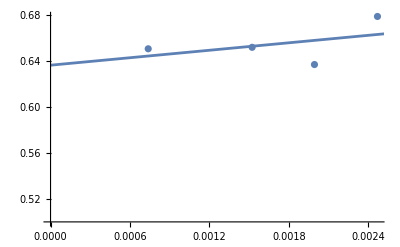

```mathematica
Show[ListPlot[data,AxesOrigin->{0,0.5}],Plot[fit[x],{x,0,10}]]
```

```mathematica
dηlst=Table[error[Hval,rlst[[i]],mlst[[i]],tlst[[i]],ρflval,dHval,drlst[[i]],dmval,dtlst[[i]],dρflval],{i,1,4}]
```

{0.0148755,0.00862724,0.00984754,0.0611092}

```mathematica
dtlst
```

{0.0894427,0.151658,0.158114,5.62832}

```mathematica
errorxplot=Table[Around[rlst[[i]],drlst[[i]]],{i,1,4}]
erroryplot=Table[Around[ηlst[[i]],dηlst[[i]]],{i,1,4}]
```

{0.0024700.000019,0.0019948,0.0015238,0.0007380.000025}

{0.6780.015,0.6370.009,0.6520.010,0.650.06}

```mathematica
graphing=SortBy[Transpose[{rlst*10^3,ηlst,drlst*10^3,dηlst}],First]
```

{{0.738,0.650284,0.0251496,0.0611092},{1.523,0.651566,0.0083666,0.00984754},{1.994,0.636608,0.00821584,0.00862724},{2.47,0.67835,0.0187083,0.0148755}}

```mathematica
boxes={#[[1]]*6*10,(#[[2]]-0.5)*100/0.1,#[[3]]*6*10,#[[4]]*100/0.1}&/@graphing
```

{{44.28,150.284,1.50897,61.1092},{91.38,151.566,0.501996,9.84754},{119.64,136.608,0.49295,8.62724},{148.2,178.35,1.1225,14.8755}}

{14.8755,8.62724,9.84754,61.1092}

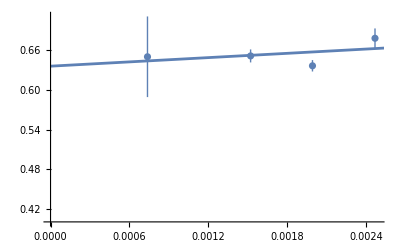

{0.545807,0.532512,0.56713,0.60672}

```mathematica
Show[ListPlot[Transpose[{errorxplot,erroryplot}],AxesOrigin->{0,0.4}],Plot[fit[x],{x,0,10}]]
```

```mathematica
Hval//N
```

0.505

## Regression

```mathematica
sumx=Total[rlst]
```

0.006725

```mathematica
sumx2=Total[#^2&/@rlst]
```

0.0000129411

```mathematica
sumy=Total[ηlst]
```

2.61681

```mathematica
sumy2=Total[#^2&/@ηlst]
```

1.71283

```mathematica
sumxy=Sum[ηlst[[i]]*rlst[[i]],{i,1,4}]
```

0.00441716

```mathematica
Length[rlst]
```

4

```mathematica
Δ= Total[1/#^2&/@ dηlst]*Sum[rlst[[i]]^2/dηlst[[i]]^2,{i,1,4}]+(Sum[rlst[[i]]/dηlst[[i]]^2,{i,1,4}])^2
```

5898.16

```mathematica
da=Sqrt[1/Δ Sum[rlst[[i]]^2/dηlst[[i]]^2,{i,1,4}]]
```

0.00422039

```mathematica
db=Sqrt[1/Δ Total[1/#^2&/@dηlst]]
```

2.19952

```mathematica
#[[1]]-#[[2]]&/@erroryplot
#[[1]]+#[[2]]&/@erroryplot
```

{0.663474,0.62798,0.641718,0.589175}

{0.693225,0.645235,0.661413,0.711393}

## Reynolds Number

```mathematica
Table[(Hval/tlst[[i]]) *(2rlst[[i]])*976/ηlst[[i]],{i,1,4}]
```

{0.229497,0.134478,0.0652737,0.00801611}

## Ladenburgkorrektur

```mathematica
correction=Table[ηlst[[i]]/((1+(2.1 rlst⟦i⟧)/(23.25/10^3)) (1+(3.3 rlst⟦i⟧)/Hval)),{i,1,4}]
```

{0.545807,0.532512,0.56713,0.60672}

```mathematica
Table[ηlst[[i]]/correction[[i]],{i,1,4}]
```

{1.24284,1.19548,1.14888,1.0718}